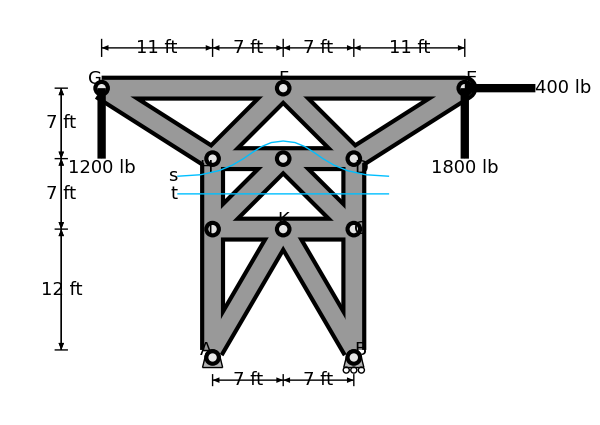

```mathematica
Module[{w1,w2,h1,h2,δh,δw},
w1=7;w2=11;h1=7;h2=12;
δh=2*h1+h2+4;δw=-w1-w2-4;


Graphics[{
{Thickness@#1,#2,
{EdgeForm@{Thickness@#1,#2},FaceForm@None,Polygon[{{-w1-w2,2*h1+h2},{w1+w2,2*h1+h2},{w1,h1+h2},{-w1,h1+h2}}]},
{Line[{{#*w1,h1+h2},{0,2*h1+h2}}],Line[{{#*w1,h2},{0,h1+h2}}],Line[{{#*w1,0},{0,h2}}]}&/@{-1,1},
Line[{{#,h1+h2},{#,0}}]&/@{-w1,w1},
Line[{{-w1,h2},{w1,h2}}]}&@@@{{0.03,Black},{0.02,GrayLevel@0.6}},

{Thick,{GrayLevel@0.7,Disk[{#*w1,-0.75},0.75],Polygon[{{#*w1-0.75,-0.75/2},{#*w1+0.75,-0.75/2},{#*w1+1,-1.75},{#*w1-1,-1.75}}]},
Line[{{#*w1-0.75,-0.75},{#*w1-1,-1.75}}],
Line[{{#*w1+0.75,-0.75},{#*w1+1,-1.75}}],
Line[{{#*w1-1,-1.75},{#*w1+1,-1.75}}],
Line@Table[{i,√(0.75^2-(i-#*w1)^2)-0.75},{i,#*w1-0.75,#*w1+0.75,0.1}]}&/@{-1,1},

{EdgeForm@Thick,FaceForm@None,Circle[{w1+#,-2},0.3]}&/@{-0.75,0,0.75},

{PointSize@0.02,Point@#,GrayLevel@0.9,PointSize@0.01,Point@#}&/@{{-w1,-0.75},{w1,-0.75},{-w1,h2},{w1,h2},{-w1,h1+h2},{w1,h1+h2},{0,h2},{0,h1+h2},{0,2*h1+h2},{-w1-w2,2*h1+h2},{w1+w2,2*h1+h2}},

(*MEASUREMENTS*)
{Arrowheads@{-0.03,0.03},
Arrow[{{0,δh},{#*w1,δh}}],
Arrow[{{#*(w1+w2),δh},{#*w1,δh}}],
Arrow[{{#*w1,-3},{0,-3}}],
Arrow[{{δw,0},{δw,h2}}],Arrow[{{δw,h2},{δw,h1+h2}}],Arrow[{{δw,h1+h2},{δw,2*h1+h2}}]
}&/@{-1,1},
Line[{{#,0.97*δh},{#,1.03*δh}}]&/@{-w1-w2,-w1,0,w1,w1+w2},
Line[{{#,-0.8*3},{#,-1.2*3}}]&/@{-w1,0,w1},
Line[{{0.97*δw,#},{1.03*δw,#}}]&/@{0,h2,h1+h2,2*h1+h2},

{Text[Style[Row@{w1," ft"},18,Background->White],{#*w1/2,δh}],Text[Style[Row@{w2," ft"},18,Background->White],{#*(w1+w2/2),δh}],Text[Style[Row@{w1," ft"},18,Background->White],{#*w1/2,-3}]}&/@{-1,1},
Text[Style[Row@{h2," ft"},18,Background->White],{δw,h2/2}],
Text[Style[Row@{h1," ft"},18,Background->White],{δw,h2+#*h1}]&/@{0.5,1.5},

{Thickness@0.01,Arrowheads@0.05,Arrow[{{#*(w1+w2),2*h1+h2},{#*(w1+w2),h1+h2}}]&/@{-1,1},
Arrow[{{w1+w2,2*h1+h2},{w1+w2+h1,2*h1+h2}}]},

Text[Style[Row@{#1," lb"},18],#2,#3]&@@@{{1200,{-w1-w2,h1+h2},{0,1.5}},{1800,{w1+w2,h1+h2},{0,1.5}},{400,{w1+w2+h1,2*h1+h2},{-1.2,0}}},

Text[Style[#1,18],#2,#3]&@@@{{"A",{-w1,0},{3.5,0}},{"B",{w1,0},{-3.5,0}},{"C",{w1,h2},{-3.5,0}},{"D",{w1,h1+h2},{-3.5,1}},{"E",{w1+w2,2*h1+h2},{-3.5,-1.5}},{"F",{0,2*h1+h2},{0,-2}},{"G",{-w1-w2,2*h1+h2},{3,-1.5}},{"H",{-w1,h1+h2},{3.5,1}},{"I",{-w1,h2},{8,0}},{"K",{0,h2},{0,-2}}},

{Thick,RGBColor[0,0.75,1],
BezierCurve[{{-1.5*w1,h2+0.75*h1},{-0.5*w1,h2+0.75*h1},{-0.5*w1,1.25*h1+h2},{0,1.25*h1+h2},{0.5*w1,1.25*h1+h2},{0.5*w1,h2+0.75h1},{1.5*w1,h2+0.75*h1}}],
Line[{{-1.5*w1,h2+0.5*h1},{1.5*w1,h2+0.5*h1}}]},

Text[Style[#1,18,Italic],{-1.5*w1,h2+#2},{2,0}]&@@@{{"s",0.75*h1},{"t",0.5*h1}}
},ImageSize->{600,425}]
]
```

```mathematica
Cyan
```

RGBColor[0, 1, 1]

```mathematica
RGBColor[0,0.75,1]
```